{N 1/2+ 0.939}

{0.932335,5.21886,{3.08276,2.96512,2.50034,2.04279}}

{0.750814,0.}

{{1.05575,-0.703836},{1.,-0.666667}}

{Δ 3/2+ 1.232}

{1.2406,5.32796,{3.08395,2.96848,2.50643,2.04279}}

{1.08401,0.766509,0.,0.766509}

{{2.15565,1.07782,0.,-1.07782},{2.04181,1.0209,0.,-1.0209}}

{Λ 1/2+ 1.116}

{1.09558,5.25524,{3.08316,2.96625,2.50238,2.04279}}

{0.17492}

{{-0.269623},{-0.255384}}

{Σ 1/2+ 1.193}

{1.13686,5.22388,{3.08282,2.96527,2.50062,2.04279}}

{0.771294,0.173462,0.731243}

{{1.02884,0.324326,-0.380186},{0.974507,0.307199,-0.360109}}

{Σ^* 3/2+ 1.385}

{1.38331,5.37677,{3.08447,2.96995,2.50912,2.04279}}

{0.794332,0.180592,0.752155}

{{1.1762,0.0885066,-0.999191},{1.11409,0.0838326,-0.946424}}

{Ξ 1/2+ 1.318}

{1.28228,5.27079,{3.08333,2.96674,2.50325,2.04279}}

{0.248397,0.716446}

{{-0.597205,-0.241786},{-0.565667,-0.229017}}

{Ξ^* 3/2+ 1.533}

{1.52892,5.42005,{3.08492,2.97123,2.51149,2.04279}}

{0.258267,0.735745}

{{0.179723,-0.91673},{0.170232,-0.868318}}

{Ω 3/2+ 1.672}

{1.67739,5.45796,{3.08532,2.97234,2.51355,2.04279}}

{0.717317}

{{-0.830956},{-0.787073}}

{π 0- 0.137}

{0.348443,4.30573,{3.07043,2.93105,2.4454,2.04279}}

{0.619446,0.619446}

{ω 1- 0.783}

{0.776444,4.54571,{3.07414,2.94117,2.46057,2.04279}}

{0.}

{{0.},{0.}}

{K 0- 0.496}

{0.561305,4.34329,{3.07103,2.9327,2.44781,2.04279}}

{0.610367,0.133749,0.133749,0.610367}

{K^* 1- 0.894}

{0.917827,4.62799,{3.07533,2.94443,2.46565,2.04279}}

{0.649532,0.146319,0.146319,0.649532}

{{0.869745,-0.0664791,0.0664791,-0.869745},{0.823814,-0.0629684,0.0629684,-0.823814}}

{ϕ 1- 1.019}

{1.06397,4.69856,{3.07631,2.94714,2.46996,2.04279}}

{0.}

{{0.},{0.}}

{Mass Spectrum}

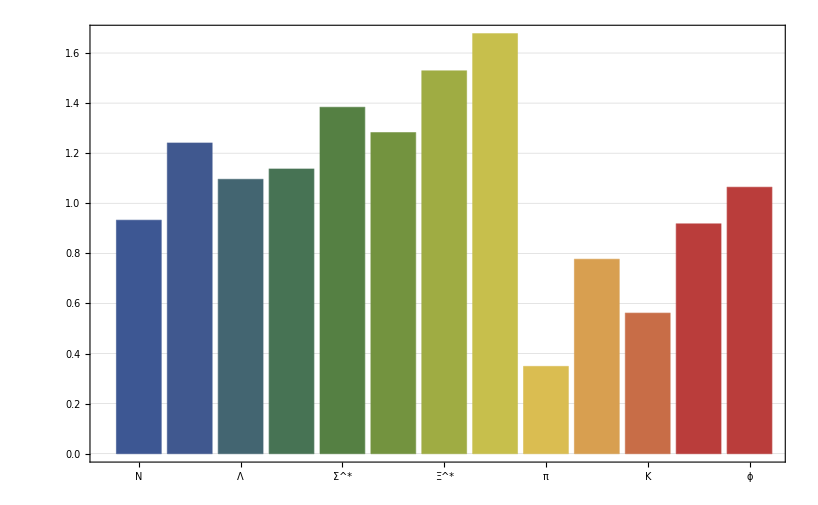

{My Error}

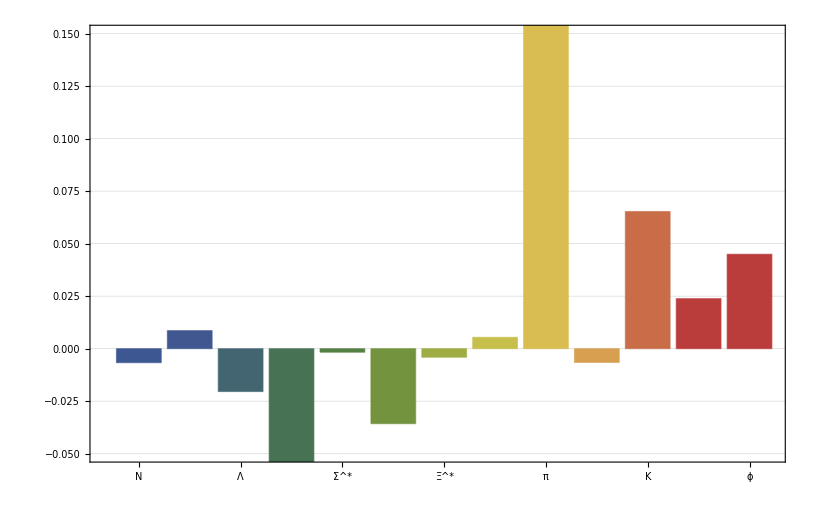

{MIT's Error}

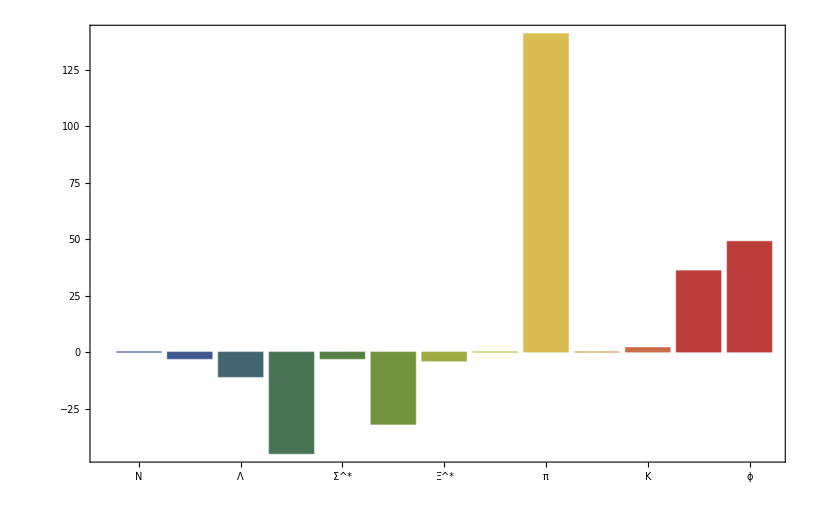

{Charge Radius}

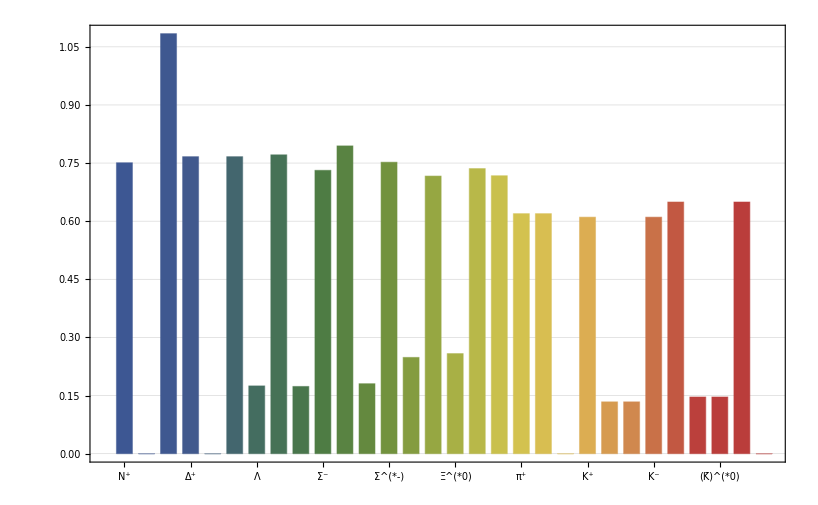

{Magnetic Moment}

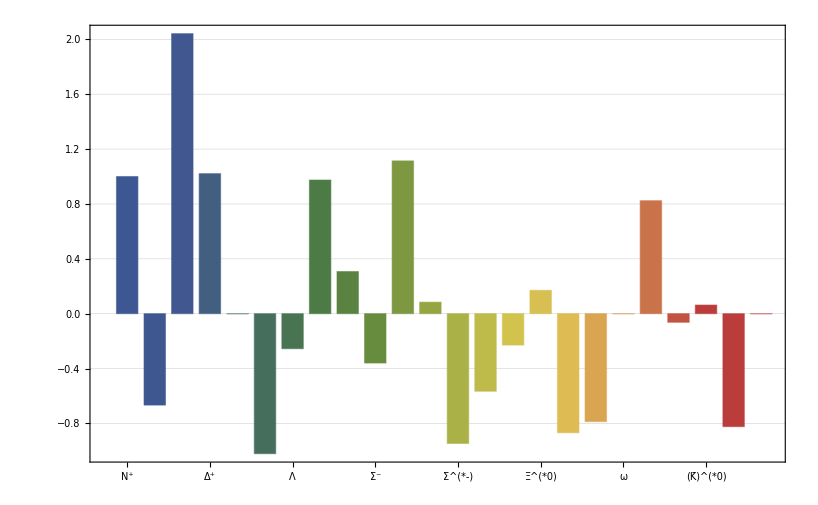

```mathematica
<<MITBagModel\MITBagModel.m

{"N 1/2+ 0.939"}
Nc=Hadron[{0,0,0,3},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,8}},0]
rNp=ChargeRadius[{0,0,0,2,1},{0,0,0,0,0},Nc];
rN0=ChargeRadius[{0,0,0,1,2},{0,0,0,0,0},Nc];
μNp=MagneticMoment[{0,0,0,4/3,-1/3},{0,0,0,0,0},Nc];
μN0=MagneticMoment[{0,0,0,-1/3,4/3},{0,0,0,0,0},Nc];
{rNp,rN0}
{{μNp,μN0},{μNp/μNp,μN0/μNp}}

{"Δ 3/2+ 1.232"}
Δ=Hadron[{0,0,0,3},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,-8}},0]
rΔpp=ChargeRadius[{0,0,0,3,0},{0,0,0,0,0},Δ];
rΔp=ChargeRadius[{0,0,0,2,1},{0,0,0,0,0},Δ];
rΔ0=ChargeRadius[{0,0,0,1,2},{0,0,0,0,0},Δ];
rΔm=ChargeRadius[{0,0,0,0,3},{0,0,0,0,0},Δ];
μΔpp=MagneticMoment[{0,0,0,3,0},{0,0,0,0,0},Δ];
μΔp=MagneticMoment[{0,0,0,2,1},{0,0,0,0,0},Δ];
μΔ0=MagneticMoment[{0,0,0,1,2},{0,0,0,0,0},Δ];
μΔm=MagneticMoment[{0,0,0,0,3},{0,0,0,0,0},Δ];
{rΔpp,rΔp,rΔ0,rΔm}
{{μΔpp,μΔp,μΔ0,μΔm},{μΔpp/μNp,μΔp/μNp,μΔ0/μNp,μΔm/μNp}}

{"Λ 1/2+ 1.116"}
Λ=Hadron[{0,0,1,2},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,8}},0]
rΛ=ChargeRadius[{0,0,1,1,1},{0,0,0,0,0},Λ];
μΛ=MagneticMoment[{0,0,1,0,0},{0,0,0,0,0},Λ];
{rΛ}
{{μΛ},{μΛ/μNp}}

{"Σ 1/2+ 1.193"}
Σ=Hadron[{0,0,1,2},{{0,0,0,0},{0,0,0,0},{0,0,0,32/3},{0,0,0,-8/3}},0]
rΣp=ChargeRadius[{0,0,1,2,0},{0,0,0,0,0},Σ];
rΣ0=ChargeRadius[{0,0,1,1,1},{0,0,0,0,0},Σ];
rΣm=ChargeRadius[{0,0,1,0,2},{0,0,0,0,0},Σ];
μΣp=MagneticMoment[{0,0,-1/3,4/3,0},{0,0,0,0,0},Σ];μΣ0=MagneticMoment[{0,0,-1/3,2/3,2/3},{0,0,0,0,0},Σ];μΣm=MagneticMoment[{0,0,-1/3,0,4/3},{0,0,0,0,0},Σ];
{rΣp,rΣ0,rΣm}
{{μΣp,μΣ0,μΣm},{μΣp/μNp,μΣ0/μNp,μΣm/μNp}}

{"Σ^* 3/2+ 1.385"}
ΣStar=Hadron[{0,0,1,2},{{0,0,0,0},{0,0,0,0},{0,0,0,-16/3},{0,0,0,-8/3}},0]
rΣpStar=ChargeRadius[{0,0,1,2,0},{0,0,0,0,0},ΣStar];
rΣ0Star=ChargeRadius[{0,0,1,1,1},{0,0,0,0,0},ΣStar];
rΣmStar=ChargeRadius[{0,0,1,0,2},{0,0,0,0,0},ΣStar];
μΣpStar=MagneticMoment[{0,0,1,2,0},{0,0,0,0,0},ΣStar];
μΣ0Star=MagneticMoment[{0,0,1,1,1},{0,0,0,0,0},ΣStar];
μΣmStar=MagneticMoment[{0,0,1,0,2},{0,0,0,0,0},ΣStar];
{rΣpStar,rΣ0Star,rΣmStar}
{{μΣpStar,μΣ0Star,μΣmStar},{μΣpStar/μNp,μΣ0Star/μNp,μΣmStar/μNp}}

{"Ξ 1/2+ 1.318"}
Ξ=Hadron[{0,0,2,1},{{0,0,0,0},{0,0,0,0},{0,0,-8/3,32/3},{0,0,0,0}},0]
rΞ0=ChargeRadius[{0,0,2,1,0},{0,0,0,0,0},Ξ];
rΞm=ChargeRadius[{0,0,2,0,1},{0,0,0,0,0},Ξ];
μΞ0=MagneticMoment[{0,0,4/3,-1/3,0},{0,0,0,0,0},Ξ];
μΞm=MagneticMoment[{0,0,4/3,0,-1/3},{0,0,0,0,0},Ξ];
{rΞ0,rΞm}
{{μΞ0,μΞm},{μΞ0/μNp,μΞm/μNp}}

{"Ξ^* 3/2+ 1.533"}
ΞStar=Hadron[{0,0,2,1},{{0,0,0,0},{0,0,0,0},{0,0,-8/3,-16/3},{0,0,0,0}},0]
rΞ0Star=ChargeRadius[{0,0,2,1,0},{0,0,0,0,0},ΞStar];
rΞmStar=ChargeRadius[{0,0,2,0,1},{0,0,0,0,0},ΞStar];
μΞ0Star=MagneticMoment[{0,0,2,1,0},{0,0,0,0,0},ΞStar];
μΞmStar=MagneticMoment[{0,0,2,0,1},{0,0,0,0,0},ΞStar];
{rΞ0Star,rΞmStar}
{{μΞ0Star,μΞmStar},{μΞ0Star/μNp,μΞmStar/μNp}}

{"Ω 3/2+ 1.672"}
Ω=Hadron[{0,0,3,0},{{0,0,0,0},{0,0,0,0},{0,0,-8,0},{0,0,0,0}},0]
rΩ=ChargeRadius[{0,0,3,0,0},{0,0,0,0,0},Ω];
μΩ=MagneticMoment[{0,0,3,0,0},{0,0,0,0,0},Ω];
{rΩ}
{{μΩ},{μΩ/μNp}}

{"π 0- 0.137"}
π0=Hadron[{0,0,0,2},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,16}},0]
rπp=ChargeRadius[{0,0,0,1,0},{0,0,0,0,1},π0];
rπm=ChargeRadius[{0,0,0,0,1},{0,0,0,1,0},π0];
{rπp,rπm}

{"ω 1- 0.783"}
ω0=Hadron[{0,0,0,2},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,-16/3}},0]
rω0=ChargeRadius[{0,0,0,1,0},{0,0,0,1,0},ω0];
μω0=MagneticMoment[{0,0,0,1,0},{0,0,0,1,0},ω0];
{rω0}
{{μω0},{μω0/μNp}}

{"K 0- 0.496"}
K=Hadron[{0,0,1,1},{{0,0,0,0},{0,0,0,0},{0,0,0,16},{0,0,0,0}},0]
rKp=ChargeRadius[{0,0,0,1,0},{0,0,1,0,0},K];
rK0=ChargeRadius[{0,0,0,0,1},{0,0,1,0,0},K];
rK0bar=ChargeRadius[{0,0,1,0,0},{0,0,0,0,1},K];
rKm=ChargeRadius[{0,0,1,0,0},{0,0,0,1,0},K];
{rKp,rK0,rK0bar,rKm}

{"K^* 1- 0.894"}
KStar=Hadron[{0,0,1,1},{{0,0,0,0},{0,0,0,0},{0,0,0,-16/3},{0,0,0,0}},0]
rKpStar=ChargeRadius[{0,0,0,1,0},{0,0,1,0,0},KStar];
rK0Star=ChargeRadius[{0,0,0,0,1},{0,0,1,0,0},KStar];
rK0barStar=ChargeRadius[{0,0,1,0,0},{0,0,0,0,1},KStar];
rKmStar=ChargeRadius[{0,0,1,0,0},{0,0,0,1,0},KStar];
μKpStar=MagneticMoment[{0,0,0,1,0},{0,0,1,0,0},KStar];
μK0Star=MagneticMoment[{0,0,0,0,1},{0,0,1,0,0},KStar];
μK0barStar=MagneticMoment[{0,0,1,0,0},{0,0,0,0,1},KStar];
μKmStar=MagneticMoment[{0,0,1,0,0},{0,0,0,1,0},KStar];
{rKpStar,rK0Star,rK0barStar,rKmStar}
{{μKpStar,μK0Star,μK0barStar,μKmStar},{μKpStar/μNp,μK0Star/μNp,μK0barStar/μNp,μKmStar/μNp}}

{"ϕ 1- 1.019"}
ϕ=Hadron[{0,0,2,0},{{0,0,0,0},{0,0,0,0},{0,0,-16/3,0},{0,0,0,0}},0]
rϕ=ChargeRadius[{0,0,1,0,0},{0,0,1,0,0},ϕ];
μϕ=MagneticMoment[{0,0,1,0,0},{0,0,1,0,0},ϕ];
{rϕ}
{{μϕ},{μϕ/μNp}}

{"Mass Spectrum"}
BarChart[{First[Nc],First[Δ],First[Λ],First[Σ],First[ΣStar],First[Ξ],First[ΞStar],First[Ω],First[π0],First[ω0],First[K],First[KStar],First[ϕ]},Frame->True,ChartLabels->{"N","Δ","Λ","Σ","Σ^*","Ξ","Ξ^*","Ω","π","ω","K","K^*","ϕ"},ChartStyle->"DarkRainbow",GridLines->Automatic,GridLinesStyle->Directive[Gray, Dashed]]

{"My Error"}
BarChart[{(First[Nc]-0.939),
(First[Δ]-1.232),
(First[Λ]-1.116),
(First[Σ]-1.193),
(First[ΣStar]-1.385),
(First[Ξ]-1.318),
(First[ΞStar]-1.533),
(First[Ω]-1.672),
(First[π0]-0.137),
(First[ω0]-0.783),
(First[K]-0.496),
(First[KStar]-0.894),
(First[ϕ]-1.019)},Frame->True,ChartLabels->{"N","Δ","Λ","Σ","Σ^*","Ξ","Ξ^*","Ω","π","ω","K","K^*","ϕ"},ChartStyle->"DarkRainbow",PlotRange->{-0.05,0.150},GridLines->Automatic,GridLinesStyle->Directive[Gray, Dashed]]

{"MIT's Error"}
BarChart[{0,-3,-11,-45,-3,-32,-4,0,141,0,2,36,49},Frame->True,ChartLabels->{"N","Δ","Λ","Σ","Σ^*","Ξ","Ξ^*","Ω","π","ω","K","K^*","ϕ"},ChartStyle->"DarkRainbow"]

{"Charge Radius"}
BarChart[{rNp,rN0,rΔpp,rΔp,rΔ0,rΔm,rΛ,rΣp,rΣ0,rΣm,rΣpStar,rΣ0Star,rΣmStar,rΞ0,rΞm,rΞ0Star,rΞmStar,rΩ,rπp,rπm,rω0,rKp,rK0,rK0bar,rKm,rKpStar,rK0Star,rK0barStar,rKmStar,rϕ},Frame->True,ChartLabels->{"N^+","N^0","Δ^(++)","Δ^+","Δ^0","Δ^-","Λ","Σ^+","Σ^0","Σ^-","Σ^(*+)","Σ^(*0)","Σ^(*-)","Ξ^0","Ξ^-","Ξ^(*0)","Ξ^(*-)","Ω","π^+","π^-","ω","K^+","K^0","(K̄)^0","K^-","K^(*+)","K^(*0)","(K̄)^(*0)","K^(*-)","ϕ"},ChartStyle->"DarkRainbow",GridLines->Automatic,GridLinesStyle->Directive[Gray, Dashed]]

{"Magnetic Moment"}
BarChart[{μNp/μNp,μN0/μNp,μΔpp/μNp,μΔp/μNp,μΔ0/μNp,μΔm/μNp,μΛ/μNp,μΣp/μNp,μΣ0/μNp,μΣm/μNp,μΣpStar/μNp,μΣ0Star/μNp,μΣmStar/μNp,μΞ0/μNp,μΞm/μNp,μΞ0Star/μNp,μΞmStar/μNp,μΩ/μNp,μω0/μNp,μKpStar/μNp,μK0Star/μNp,μK0barStar/μNp,μKmStar/μNp,μϕ/μNp},Frame->True,ChartLabels->{"N^+","N^0","Δ^(++)","Δ^+","Δ^0","Δ^-","Λ","Σ^+","Σ^0","Σ^-","Σ^(*+)","Σ^(*0)","Σ^(*-)","Ξ^0","Ξ^-","Ξ^(*0)","Ξ^(*-)","Ω","ω","K^(*+)","K^(*0)","(K̄)^(*0)","K^(*-)","ϕ"},ChartStyle->"DarkRainbow",GridLines->Automatic,GridLinesStyle->Directive[Gray, Dashed]]
```